# Cental Force F⃗ = r⃗ f[r]

## General Theory

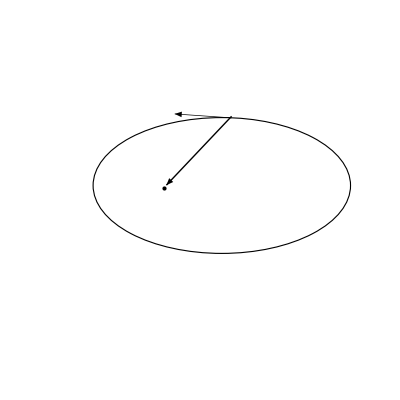

### Force

```mathematica
r^(->)=r r^⋀
r^⋀={Cos[θ],Sin[θ]}
θ^⋀={-Sin[θ],Cos[θ]}
OverDot[r^⋀]=θ̇ θ^⋀
OverDot[θ^⋀]=-θ̇ r^⋀
OverDot[r^(->)]=ṙ r^⋀+r θ̇ θ^⋀
(r^(->))^(..)=(r^(..)-r (θ̇)^2)r^⋀+(2 ṙ θ̇+r θ^(..))θ^⋀=(r^(..)-r (θ̇)^2)r^⋀+1/r(ⅆ(r^2 θ̇))/ⅆt θ^⋀
```

```mathematica
(* the angular part of Force = 0*)
0 =m 1/r(ⅆ(r^2 θ̇))/ⅆt ⇒ r^2 θ̇=l/m⇒ θ̇=l/(m r^2)⇒ (θ̇)^2=l^2/(m^2 r^4)
```

```mathematica
(* the radial part of Force = F[r]=-(ⅆ V[r])/ⅆr*)
-(ⅆ V[r])/ⅆr=m(r^(..)-r (θ̇)^2)=m ( (ⅆ (1/2(ṙ)^2))/(ⅆ r)-l^2/(m^2 r^3))
(ⅆ (1/2 ṙ+ V[r]/m))/(ⅆ r)=l^2/(m^2 r^3)
(ṙ)^2+l^2/(m^2 r^2) +2/m V[r]=Cont
```

```mathematica
Manipulate[Plot[α/r^2-β/r,{r,0,10}],{α,0,1},{β,0,1}]
```

### Energy

```mathematica
(* Central Force F depends on r, thus the cross product with r is Zero *)
r×F=0
(* From 
r×F=0
r×(ⅆ p)/(ⅆ t) = 0
(ⅆ L)/(ⅆ t)= p × (ⅆ r)/(ⅆ t) = p × v = 0
 Thus, Angular momentum is a constant with time *)
(* or simply by Torque Zero *)
l = Constant
m r^2 ⅆθ/ⅆt=Constant=l
ⅆθ/ⅆt=l/(m r^2)
(* The Total Mechanical Energy equals to K.E. + P.E. *)
(* The K.E. = Radial + Angular part *)
E= m/2(ⅆr/ⅆt)^2+m/2 r^2(ⅆθ/ⅆt)^2+V[r]
E=m/2(ⅆr/ⅆt)^2+l^2/(2m r^2)+V[r]
```

```mathematica
(* Define a kinetic P.E., which is the angular part of K.E. *)
Vkin[r_]=l^2/(2m r^2);
```

```mathematica
(* If we set F = k m r^n *)
V[r_]=(m k r^(n+1))/(n+1);
```

### Potential Poltting

```mathematica
(* Ploting  the Effective P.E. for differnt demension "n" *)
Manipulate[
Plot[{l^2/(2m r^2),k m r^(n+1)/(n+1),l^2/(2m r^2)+k m r^(n+1)/(n+1),ME}
,{r,0,10},PlotRange->{{0,3},{-3,3}},
Epilog->{
Arrow[{{1.5,1},{1,l^2/(2m)}}],Text["V kin / K.E. Radial",{1.5,1},{-1,-1}],
Arrow[{{2.5,1},{2,k m 2^(n+1)/(n+1)}}],Text["V Real",{2.5,1},{-1,-1}],
Arrow[{{1,2},{0.3,l^2/(2m 0.3^2)+k m 0.3^(n+1)/(n+1)}}],Text["V eff",{1,2},{-1,-1}],
Arrow[{{2,-2.5},{1.5,ME}}],Text["Total Energy",{2,-2.5},{-1,-1}]
}
]
,{m,1,100},{{l,1},0,10},{{k,2},-10,10},{ME,-2,2},{{n,-2},-4,2}]
```

```mathematica
Manipulate[
RevolutionPlot3D[
{l^2/(2m r^2)+(k m r^(n+1))/(n+1)}
,{r,0,10},RegionFunction -> Function[{x,y,z}, x^2+y^2>1/10]
]
,{m,1,100},{l,1,10},{{k,0.5},0,10},{ME,-2,2},{{n,-2},-4,2}]
```

## Energy

```mathematica
(* The Range of Bounded orbit , Mini ME *)
D[l^2/(2m r^2)+k m r^(n+1)/(n+1),r]
Solve[D[l^2/(2m r^2)+k m r^(n+1)/(n+1),r]==0,r]
```

-l^2/(m r^3)+k m r^n

{{r→((k m^2)/l^2)^(1/(-3-n))}}

```mathematica
(* Mini ME *)
l^2/(2m r^2)+k m r^(n+1)/(n+1)/.{r->((k m^2)/l^2)^(1/(-3-n))}//Simplify
%/.{n->-2}
```

1/2 k m ((k m^2)/l^2)^(-1+2/(3+n))+(k m (((k m^2)/l^2)^(-1/(3+n)))^(1+n))/(1+n)

-(k^2 m^3)/(2 l^2)

```mathematica
(* Solve for Intersection  For n = -2 *)

Solve[(l^2/(2m r^2)+(k m r^(n+1))/(n+1)==ME)/.{n->-2},r]
```

{{r→(-k m^2-√(k^2 m^4+2 l^2 m ME))/(2 m ME)},{r→(-k m^2+√(k^2 m^4+2 l^2 m ME))/(2 m ME)}}

```mathematica
-(k m)/(2 ME)(1±√(1+(2 l^2)/(k^2 m^3) ME))
(* Thus, For real root *)
 ME≥-(k^2 m^3)/(2 l^2)
(* See below result *)
```

## General Solution

```mathematica
(* Central froce, k>0 = Attractive *)
F[r_,n_]:=k m  r^n;
Vkin[r]=l^2/(2 m r^2);
V[r,n]=Integrate[F[r,n],r]
```

(k m r^(1+n))/(1+n)

```mathematica
(* Effective P.E. *)
Veff[r_,n_]=V[r,n]+Vkin[r]
```

l^2/(2 m r^2)+(k m r^(1+n))/(1+n)

```mathematica
(* Total Mechanics Energy *)
ME=m/2(ⅆr/ⅆt)^2+l^2/(2m r^2)+(m k r^(1+n))/(1+n)
ⅆr/ⅆt=ⅆr/ⅆθ ⅆθ/ⅆt=ⅆr/ⅆθ l/(m r^2)
ME==l^2/(2m r^4)(ⅆr/ⅆθ)^2+l^2/(2m r^2)+(m k r^(1+n))/(1+n)
ME==l^2/(2m r^4)(ⅆr/ⅆθ)^2+V
(* For circular orbit ,ⅆr/ⅆθ = 0, the radial part is zero, and all ME is due to angular part *)
```

```mathematica
Solve[ME==l^2/(2m r^4)(1/x)^2+V,x]
```

{{x→-l/(√(2 m ME r^4-2 m r^4 V))},{x→l/(√(2 m ME r^4-2 m r^4 V))}}

```mathematica
(* solve out (ⅆ θ)/(ⅆ r) *)
Solve[ME==l^2/(2m r^4)(1/x)^2+l^2/(2m r^2)+(m k r^(1+n))/(1+n),x]
```

{{x→-(√(-l^2-l^2 n))/(√(l^2 r^2+l^2 n r^2-2 m ME r^4-2 m ME n r^4+2 k m^2 r^(5+n)))},{x→(√(-l^2-l^2 n))/(√(l^2 r^2+l^2 n r^2-2 m ME r^4-2 m ME n r^4+2 k m^2 r^(5+n)))}}

```mathematica
(* The solution is *)
θ=∫(√(-l^2-l^2 n))/(√(l^2 r^2+l^2 n r^2-2 m ME r^4-2 m ME n r^4+2 k m^2 r^(5+n)))ⅆr
(* the Free parameters are 

ME = Mechanical Energy
l = angular velocity
*)
```

## Gravity ( n = - 2 )

```mathematica
Veff[r,-2]
```

l^2/(2 m r^2)-(k m)/r

```mathematica
(* the equation for energy *)
ME=m/2(ⅆr/ⅆt)^2+Veff[r,-2]
```

### Solution

```mathematica
(* For n=-2 *)
Refine[Simplify[(√(-l^2-l^2 n))/(√(l^2 r^2+l^2 n r^2-2 m ME r^4-2 m ME n r^4+2 k m^2 r^(5+n)))/.n->-2], {r>0,l>0}]
```

l/(r √(-l^2+2 m r (k m+ME r)))

```mathematica
(* the direct integration is not nice *)
(* use r -> 1/u *)
FullSimplify[l/(r √(-l^2+2 m r (k m+ME r)))/.{r->1/u} ]D[1/u,u]//Simplify
```

-l/(u √(-l^2+(2 m (ME+k m u))/u^2))

```mathematica
(* Further simplify *)
1/(√(-u^2+(k 2 m^2 u)/l^2+(2 m ME)/l^2))/.{ME->(c l^2)/(2 m),k->(b l^2)/(2 m^2)}
```

1/(√(c+b u-u^2))

```mathematica
(* The initial condition *)
∫1/(√(c+b u-u^2))ⅆu
```

-ArcTan[((-b+2 u) √(c+b u-u^2))/(2 (-c-b u+u^2))]

```mathematica
Refine[Refine[Solve[θ==ArcTan[((-b+2 u) √(c+b u-u^2))/(2 (-c-b u+u^2))],u]//FullSimplify,Sec[θ]>0],Tan[θ]>0]
```

{{u→1/2 (b-√(b^2+4 c) Sin[θ])},{u→1/2 (b+√(b^2+4 c) Sin[θ])}}

```mathematica
(* Subsitite back *)
1/2 (b+√(b^2+4 c) Sin[θ])/.{b->(k 2 m^2)/l^2 ,c->(2 m ME)/l^2}//Simplify
```

(k m^2)/l^2+√((k^2 m^4+2 l^2 m ME)/l^4) Sin[θ]

```mathematica
r=(l^2/(k m^2))/(1+√(1+(2 l^2  ME)/(k^2 m^3)) Sin[θ])
(* For Ellipse, l^2/(k m^2) is the size of the orbit *)
r = p/(1+ϵ Sin[θ]) (* form of Conice section*)

(* for k > 0 ⇒ attractive force *)
ME = l^2/(2m r^4)(ⅆr/ⅆθ)^2+l^2/(2m r^2)-(m k)/r
(* Ellipse , 0 < ϵ < 1 *)
-(k^2 m^3)/(2 l^2)<ME < 0    (* possible since k > 0, the potential term creates negative *)
(* Parabola ϵ = 1 *)
ME = 0
(* Hyperbola ,0 < ϵ < 1 *)
ME > 0
(* For k < 0 ⇒ repulsive force *)
(* the potential term also positive, *)
ME > 0 ⇒ Hyperbola
```

### Matching with Ellipse

```mathematica
(* a typical ellipse has equation *)
r = (a (1-ϵ^2))/(1+ϵ Sin[θ])
```

```mathematica
Solve[{l^2/(k m^2)== a(1-ϵ^2),ϵ==√(1+(2 l^2  ME)/(k^2 m^3))},{a,ϵ}]//Simplify
```

{{a→-(k m)/(2 ME),ϵ→√(1+(2 l^2 ME)/(k^2 m^3))}}

```mathematica
(* for the major semi-axis *)
a=-(k m)/(2 ME)
(* ME is negative for ellitoc orbit *)
a = (k m)/(2 Abs[ME])
```

```mathematica
Manipulate[
Plot[{l^2/(2m r^2),k m r^(n+1)/(n+1),l^2/(2m r^2)+k m r^(n+1)/(n+1),ME, -(k m)/(2 r)}
,{r,0,10},PlotRange->{{0,3},{-3,3}},
Epilog->{
Arrow[{{1.5,1},{1,l^2/(2m)}}],Text["V kin / K.E. Radial",{1.5,1},{-1,-1}],
Arrow[{{2.5,1},{2,k m 2^(n+1)/(n+1)}}],Text["V Real",{2.5,1},{-1,-1}],
Arrow[{{1,2},{0.3,l^2/(2m 0.3^2)+k m 0.3^(n+1)/(n+1)}}],Text["V eff",{1,2},{-1,-1}],
Arrow[{{2,-2.5},{1.5,ME}}],Text["Total Energy",{2,-2.5},{-1,-1}],
Arrow[{{1,-3},{0.75,-(k m)/(2 0.75)}}],Text["The mean distance ",{1,-3},{-1,-1}]
}
]
,{m,1,100},{{l,1},0,10},{{k,2},-10,10},{ME,-2,2},{{n,-2},-4,2}]
```

### ϵ = 0 , ME = -(k^2 m^3)/(2 l^2)

```mathematica
(* For a circle ϵ = 0 *)
Solve[√(1+(2 l^2 ME)/(k^2 m^3))==0,ME]
```

{{ME→-(k^2 m^3)/(2 l^2)}}

```mathematica
(* Compare to Simple force balancing *)
Fg= (k m)/a^2= (m v^2)/a=Fc ⇒ k = a v^2 = l^2/(m^2 a) ⇒ a = l^2/(k m^2)
ME= (m v^2)/2-(k m)/a= l^2/(2 m a^2)-(k^2 m^3)/l^2=-(k^2 m^3)/(2 l^2)=- (k m)/(2 a^2)
(* agree *)
```

### Speed on θ @ nerest and farest point

```mathematica
(* Solution is *)
r=(l^2/(k m^2))/(1+√(1+(2 l^2  ME)/(k^2 m^3)) Sin[θ])
```

```mathematica
(* At nearest or farest point *)
(ⅆ r)/(ⅆ t)==0
(* the radial velocity is Zero *)
(* The Total Mechanical Energy is angular term + potential term *)
ME = l^2/(2 m r^2)-(k m)/r= 1/2 m r^2 ω^2- (k m)/r
(* For nearest point,  a->-(k m)/(2 ME),ϵ->√(1+(2 l^2 ME)/(k^2 m^3)), r = a (1-ϵ)*)
r = -(k m)/(2 ME)(1-√(1+(2 l^2)/(k^2 m^3) ME))
```

```mathematica
Solve[ME == 1/2 m r^2 ω^2- (k m)/r,ω]/.r ->  a(1±ϵ)//Simplify
```

{{ω→-(√2 √(ME+(k m)/(a (1±ϵ))))/(a √m (1±ϵ))},{ω→(√2 √(ME+(k m)/(a (1±ϵ))))/(a √m (1±ϵ))}}

```mathematica
SubMinus[ω]=(√2 √(ME+(k m)/(a (1-ϵ))))/(a √m (1-ϵ));SubPlus[ω]=(√2 √(ME+(k m)/(a (1+ϵ))))/(a √m (1+ϵ));
SubMinus[ω]/SubPlus[ω]//Simplify
```

-((1+ϵ) √(ME+(k m)/(a-a ϵ)))/((-1+ϵ) √(ME+(k m)/(a+a ϵ)))

```mathematica
(* For ϵ = 0, circluar orbit, the angular speed are equal *)
```

### Changing Orbit

```mathematica
(* Chnageing orbit is equal to equate the 2 orbit at some angle ϕ *)
(a1(1-ϵ1^2))/(1+ϵ1 Cos[ϕ+θ1])==(a2(1-ϵ2^2))/(1+ϵ2 Cos[ϕ+θ2])
```

```mathematica
(* The easiest way to change orbit from 1 to another, is adding thrust on the point r'[t]==0 *)
(* i.e. ϕ = 0 or π and θ1 = θ2 = 0 *)
a1(1∓ϵ1)==a2(1∓ϵ2)
(* - for ϕ=0, + for ϕ = π *)
a(1+(-1)^n ϵ) (* n = 2 , ϕ = π ; n = 1, ϕ = 0 *)
```

```mathematica
(* Let β be the change of velocity at that point *)
v2=β v1
(* since r'[t]=0*)
ME = l^2/(2m r^2)-(m k)/r=1/2 m v^2-(m k)/(a(1∓ϵ))
(* recall that *)
a=-(k m)/(2 ME) (* or *) ME = -(m k)/(2 a)
```

```mathematica
Solve[-(m k)/(2 a)==1/2 m v^2-(m k)/(a(1+(-1)^n ϵ)),v]//Simplify
```

{{v→-√((k-(-1)^n k ϵ)/(a+(-1)^n a ϵ))},{v→√((k-(-1)^n k ϵ)/(a+(-1)^n a ϵ))}}

```mathematica
Solve[√((1-(-1)^n  ϵ2)/(a2(1+(-1)^n  ϵ2)))==β √((1-(-1)^n  ϵ1)/(a1(1+(-1)^n ϵ1))),β]//FullSimplify
```

{{β→(√((1-(-1)^n ϵ2)/(a2+(-1)^n a2 ϵ2)))/(√((1-(-1)^n ϵ1)/(a1+(-1)^n a1 ϵ1)))}}

```mathematica
β=√((1-((-1)^n ϵ2))/(1-((-1)^n ϵ1)) a1/a2(1++((-1)^n ϵ1))/(1+((-1)^n ϵ2)))(* For nearest point n = 1, farest point n = 2*)
```

```mathematica
(* For example *)
(* From a circlar orbit r = R1, to r = R2, via and ellipse *)
(* we have a intermediate ellipse with a and ϵ *)
Solve[{R1 == a(1-ϵ),R2 == a (1+ϵ)},{a,ϵ}]
```

{{ϵ→(-R1+R2)/(R1+R2),a→(R1+R2)/2}}

```mathematica
β1=√((1-((-1)^n ϵ2))/(1-((-1)^n ϵ1)) a1/a2(1++((-1)^n ϵ1))/(1+((-1)^n ϵ2)))/.{ϵ2->(-R1+R2)/(R1+R2),a2->(R1+R2)/2,ϵ1->0,a1->R1,n->1}//Simplify
β2=√((1-((-1)^n ϵ2))/(1-((-1)^n ϵ1)) a1/a2(1++((-1)^n ϵ1))/(1+((-1)^n ϵ2)))/.{ϵ1->(-R1+R2)/(R1+R2),a1->(R1+R2)/2,ϵ2->0,a2->R2,n->0}//Simplify
(* For R2 = 2 R1 *)
β1/.{R2->2 R1}//N
β2/.{R2->2 R1}//N
```

√2 √(R2/(R1+R2))

(√((R1+R2)/R1))/(√2)

1.1547

1.22474

```mathematica
(* If we solve the speed *)
v1 = √((k-(-1)^n k ϵ)/(a+(-1)^n a ϵ))/.{ϵ->0,a->R1};
v2=√((k-(-1)^n k ϵ)/(a+(-1)^n a ϵ))/.{ϵ->0,a->R2};
v2/v1/.{R2->2R1}//N
```

0.707107

```mathematica
(* The speed actually slower *)
(* The energy spent on against the gravity and then trabsfered to the gravitational portential *)
vNear = β1 v1//Simplify
(* The potential energy gained *)
vFar=s/.Solve[1/2 m vNear^2-(m k)/R1==1/2 m s^2-(m k)/R2,s][[2]]//Simplify
v2 = β2 vFar//Simplify
{v1,vNear,vFar,v2}/.{R2->2 R1}//N
```

√2 √(k/R1) √(R2/(R1+R2))

√2 √((k R1)/(R2 (R1+R2)))

√((k R1)/(R2 (R1+R2))) √((R1+R2)/R1)

{√(k/R1),1.1547 √(k/R1),0.57735 √(k/R1),0.707107 √(k/R1)}

### Other things

```mathematica
(* Find the θ[t] *)
(* Since 0< ϵ < 1, replace ϵ = Sin[ϕ] *)
∫1/(1+ϵ Cos[θ])^2 ⅆθ
```

-(2 ArcTanh[((-1+ϵ) Tan[θ/2])/(√(-1+ϵ^2))])/((-1+ϵ^2)^(3/2))+(ϵ Sin[θ])/((-1+ϵ^2) (1+ϵ Cos[θ]))

```mathematica
Manipulate[
Plot[-(2 ArcTanh[((-1+ϵ) Tan[θ/2])/(√(-1+ϵ^2))])/((-1+ϵ^2)^(3/2))+(ϵ Sin[θ])/((-1+ϵ^2) (1+ϵ Cos[θ])),{ϵ,0,1}, PlotRange->4,AxesLabel->{ϵ,t}]
,{{θ,0.5},-π,π}]
```

```mathematica
(* Plot t[θ] *)
Manipulate[
Plot[-(2 ArcTanh[((-1+ϵ) Tan[θ/2])/(√(-1+ϵ^2))])/((-1+ϵ^2)^(3/2))+(ϵ Sin[θ])/((-1+ϵ^2) (1+ϵ Cos[θ])),{θ,-π,π}, PlotRange->4,AxesLabel->{θ,t}]
,{{ϵ,0.5},0,1}]
```

```mathematica
(* Numerical Solve *)
-(2 ArcTanh[((-1+ϵ) Tan[θ/2])/(√(-1+ϵ^2))])/((-1+ϵ^2)^(3/2))+(ϵ Sin[θ])/((-1+ϵ^2) (1+ϵ Cos[θ]))/.ϵ->0.5
```

(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])

```mathematica
Table[{t,NSolve[(-(2 ArcTanh[((-1+ϵ) Tan[θ/2])/(√(-1+ϵ^2))])/((-1+ϵ^2)^(3/2))+(ϵ Sin[θ])/((-1+ϵ^2) (1+ϵ Cos[θ]))/.ϵ->0.5)==t,θ]},{t,0,1,0.1}]
```

{{0.,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.,θ]},{0.1,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.1,θ]},{0.2,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.2,θ]},{0.3,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.3,θ]},{0.4,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.4,θ]},{0.5,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.5,θ]},{0.6,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.6,θ]},{0.7,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.7,θ]},{0.8,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.8,θ]},{0.9,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==0.9,θ]},{1.,NSolve[(3.0792+0. ⅈ) ArcTan[(0.57735+0. ⅈ) Tan[θ/2]]-(0.666667 Sin[θ])/(1+0.5 Cos[θ])==1.,θ]}}

```mathematica
Manipulate[
Animate[
ParametricPlot[{Cos[ϕ]/(1+ ϵ Cos[ϕ])+(2ϵ)/(1-ϵ^2), Sin[ϕ]/(1+ ϵ Cos[ϕ])},{ϕ,j-0.5,j}, PlotRange->4,
Epilog->{
Arrow[{{0,0},{Cos[j]/(1+ ϵ Cos[j])+(2ϵ)/(1-ϵ^2), Sin[j]/(1+ ϵ Cos[j])}}],
Arrow[{{(2ϵ)/(1-ϵ^2),0},{Cos[j]/(1+ ϵ Cos[j])+(2ϵ)/(1-ϵ^2), Sin[j]/(1+ ϵ Cos[j])}}]
}]
,{j,0,2π}]
,{{ϵ,0.5},0,1}]
```

```mathematica
(* D[r,{t,2}] *)
Dr=D[l^2/(1+√(1+2 l^2  ME) Sin[θ[t]]),{t,1}]/.θ'[t]->1/l^3(1+√(1+2 l^2  ME) Sin[θ[t]])^2//Expand//Simplify
DDr=D[%,t]/.θ'[t]->1/l^3(1+√(1+2 l^2  ME) Sin[θ[t]])^2//Expand//Simplify
```

-(√(1+2 l^2 ME) Cos[θ[t]])/l

(Sin[θ[t]] (√(1+2 l^2 ME)+(2+4 l^2 ME) Sin[θ[t]]+(1+2 l^2 ME)^(3/2) Sin[θ[t]]^2))/l^4

```mathematica
(* r (θ̇)^2 *)
rDθ2=l^2/(1+√(1+2 l^2  ME) Sin[θ[t]]) l^2/((l^2/(1+√(1+2 l^2  ME) Sin[θ[t]]))^4)//Simplify
```

((1+√(1+2 l^2 ME) Sin[θ[t]])^3)/l^4

```mathematica
(* The radial acceleration *)
DDr-rDθ2//FullSimplify
```

-(1+2 √(1+2 l^2 ME) Sin[θ[t]]+(1+2 l^2 ME) Sin[θ[t]]^2)/l^4

```mathematica
(* should be equal to 1/r^2 *)
1/(l^2/(1+√(1+2 l^2  ME) Sin[θ[t]]))^2//Simplify
```

((1+√(1+2 l^2 ME) Sin[θ[t]])^2)/l^4

```mathematica
Manipulate[
PolarPlot[(1+2 √(1+2 l^2 ME) Sin[θ]+(1+2 l^2 ME) Sin[θ]^2)/l^4,{θ,0,2π}]
,{ME,-3,0},{l,0.1,4}]
```

```mathematica
rDθ=l^2/(1+√(1+2 l^2  ME) Sin[θ[t]]) l/((l^2/(1+√(1+2 l^2  ME) Sin[θ[t]]))^2)//Simplify
```

(1+√(1+2 l^2 ME) Sin[θ[t]])/l

```mathematica
(* From this *)
E=m/2(ⅆr/ⅆt)^2+l^2/(2m r^2)+V[r]
t = √(m/2)∫ⅆr/(√(E-l^2/(2m r^2)-V[r]))
```

```mathematica
∫ⅆr/(√(ME-l^2/(2m r^2)-(k m)/r))//Simplify
```

1/(2 m ME^(3/2) r √(2 ME-(l^2+2 k m^2 r)/(m r^2)))(√2 √ME (-l^2+2 m r (-k m+ME r))+k m^(3/2) √(-l^2+2 m r (-k m+ME r)) Log[-2 k m^2+4 m ME r+2 √2 √m √ME √(-l^2+2 m r (-k m+ME r))])

```mathematica
1/(√(ME-l^2/(2m r^2)-(k m)/r))//Expand//Simplify
```

1/(√(ME-(l^2+2 k m^2 r)/(2 m r^2)))

```mathematica
1/(√(ME-(l^2+2 k m^2 r)/(2 m r^2)))==(√(2m)r)/(√(ME 2m r^2-l^2-2 k m^2 r))
```

```mathematica
∫(√(2m)r)/(√(ME 2m r^2-l^2-2 k m^2 r))ⅆr
(* 
a^2= 2 m ME
2 a b = 2 k^2 m
*)
```

```mathematica
Solve[{a^2== 2 m ME,2 a b == 2 k m^2},b]
```

{{b→(k m^2)/a}}

```mathematica
r/(√(ME 2m r^2-l^2-2 k m r))==r/(√(ME 2m r^2-2 k m r+(k^2 m^3)/(2 ME)-((k^2 m^3)/(2 ME)+l^2)))==r/(√((a r-b)^2-c))
a = √(2 m ME)
b = (k √m)/(√(2 ME))
c = (k^2 m^3)/(2 ME)+l^2
```

```mathematica
Solve[(k^2 m^3)/(2 ME)+l^2==0,ME]
```

{{ME→-(k^2 m^3)/(2 l^2)}}

```mathematica
(* whihc is a circle *)
```

```mathematica
∫r/(a r-b )ⅆr
```

r/a+(b Log[-b+a r])/a^2

```mathematica
a r+b Log[-b+a r]==t a^2
Exp[a r] (a r -b)^b== Exp[t a^2]
```

```mathematica
Exp[(√(-c+(b-a r)^2)-a^2 t)/b]==2 (b-a r+√(-c+(b-a r)^2))
```

```mathematica
(* when t = 0, r = α *)
```

## The velocity vector and accelration vector during motion

```mathematica
r
Dr
rDθ
```

l^2/(1+√(1+2 l^2 ME) Sin[θ+θ0])

-(√(1+2 l^2 ME) Cos[θ[t]])/l

(1+√(1+2 l^2 ME) Sin[θ[t]])/l

## Given a point and a velocity, calculate back the orbit

```mathematica
Manipulate[PolarPlot[1/(1+ϵ Cos[θ+θ0]),{θ,0,2π}],{ϵ,0,1},{θ0,0 ,π}]
```

```mathematica
(* The general equation *)
r=l^2/(1+√(1+2 l^2  ME) Sin[θ+θ0])
(* l and ME can be found *)
```

l^2/(1+√(1+2 l^2 ME) Sin[θ+θ0])

{{θ0→ArcSin[(-√(1+2 l^2 ME)+(l^2 √(1+2 l^2 ME))/pr)/(1+2 l^2 ME)]}}

```mathematica
(* a give point, clindrical symmetry, only radial position is needed *)
pr;
(* the velocity, the radial part and anugular part *)
pv ;
pvθ=90°;
```

```mathematica
(* the angular velocity *)
pl=pr pv Sin[pvθ];
(* ME *)
pME =1/2(pv)^2-1/pr;
(* θ0 *)
Solve[pr == pl^2/(1+√(1+2 pl^2  pME) Cos[θ0]),θ0,InverseFunctions->True]
(* ϵ *)
pϵ = √(1+2 pl^2  pME) //Simplify

pl^2/(1+pϵ Cos[θ+θ0])//Simplify
```

{{θ0→-ArcCos[(-√((-1+pr pv^2)^2)+pr pv^2 √((-1+pr pv^2)^2))/(1-2 pr pv^2+pr^2 pv^4)]},{θ0→ArcCos[(-√((-1+pr pv^2)^2)+pr pv^2 √((-1+pr pv^2)^2))/(1-2 pr pv^2+pr^2 pv^4)]}}

√((-1+pr pv^2)^2)

(pr^2 pv^2)/(1+√((-1+pr pv^2)^2) Cos[θ+θ0])

```mathematica
Manipulate[PolarPlot[(pr^2 pv^2)/(1+√((-1+pr pv^2)^2) Cos[θ+ArcCos[(-√((-1+pr pv^2)^2)+pr pv^2 √((-1+pr pv^2)^2))/(1-2 pr pv^2+pr^2 pv^4)]]),{θ,0,2π},PlotRange->1,
Epilog->{Arrow[{{pr,0},{pr+pv Cos[pvθ],pv Sin[pvθ]}}]}
],{{pr,0.5},0,1},{{pv,0.5},0,10},{{pvθ,π/2},0,π}]
```